## matrix-count_tests

Versions of the estimates to test, also validation on test cases that the moments indeed match

### Functions

```mathematica
logBinom[a_,b_]:=LogGamma[a+1]-LogGamma[b+1]-LogGamma[a-b+1]
```

## test_util

### _log_weight

```mathematica
Module[{mat,α},mat={{2,2,3},{2,3,4},{3,4,4}};α=5;Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}]]//N//Log
```

17.0292

## test_estimate.py

### alpha_symmetric_2

#### diagonal_sum = None

```mathematica
αSymmetric2NoDiag[T_,n_,α_]:=(-((1+n)*(2+n))+T*(2+n*(2+n)))/((-2+n)*(1+n)+T*(2+n))
```

```mathematica
αSymmetric2NoDiag[200,10,1]//N
```

9.75402

```mathematica
αSymmetric2NoDiag[200,10,5]//N
```

41.168

```mathematica
logSymmetric2NoDiag[ks_,α_]:=Module[{T,n,αDM},T=Total[ks];n=Length[ks];αDM=αSymmetric2NoDiag[T,n,α];logBinom[T/2 +α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αDM - 1, n αDM - 1]  + Total[logBinom[ks+αDM - 1, αDM - 1]]]
```

```mathematica
logSymmetric2NoDiag[{20,11,3},1]//N//Exp
```

38.7629

```mathematica
logSymmetric2NoDiag[{20,11,3},1]//N
```

3.65746

```mathematica
logSymmetric2NoDiag[{20,11,3},5]//N
```

20.3397

#### diagonal_sum

```mathematica
αSymmetric2Diag[T_,Td_,n_,α_]:=-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))
```

```mathematica
αSymmetric2Diag[200,100,10,1]//N
```

3.6041

```mathematica
αSymmetric2Diag[200,100,10,5]//N
```

13.1526

```mathematica
αSymmetric2Diag[200,100,0.00001,5]//N
```

101012.

```mathematica
αSymmetric2Diag[200,100,200.,5]//N
```

1.81507

```mathematica
logSymmetric2Diag[ks_,diagSum_,α_]:=Module[{T,n,αDM},T=Total[ks];n=Length[ks];αDM=αSymmetric2Diag[T,diagSum,n,α]; logBinom[diagSum/2 + α n - 1,α n - 1]+logBinom[(T-diagSum)/2 + α n*(n-1)/2 - 1,α n*(n-1)/2 - 1] -logBinom[T + n αDM - 1, n αDM - 1] + Total[logBinom[ks+αDM - 1, αDM - 1]]]
```

```mathematica
logSymmetric2Diag[{20,11,3},20,1]//N//Exp
```

3.65095

```mathematica
logSymmetric2Diag[{20,11,3},20,1]//N
```

1.29499

```mathematica
logSymmetric2Diag[{20,11,3},20,5]//N
```

18.5925

If the diagonal sum is 0, we simplify since this case is often used in sequential importance sampling

```mathematica
αSymmetric2Diag[T,0,n,α]//Simplify
```

(-((2-3 n+n^2) α)+T (1+(-1+n)^2 α))/(2-2 T-n^2 α+n (-2+T+α))

```mathematica
(-((2-3 n+n^2) α)+T (1+(-1+n)^2 α))/(2-2 T-n^2 α+n (-2+T+α))/.{T->10,α->1.00001,n->6}
```

-800008.

```mathematica
αSymmetric2Diag[2*tmOut,0,Length[diagonalSum],1+0.00001]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
logSymmetric2Diag[{2,2,2,2,1,1},0,1.0001]
```

3.77589+0. ⅈ

### alpha_symmetric_3

#### diagonal_sum = None

```mathematica
αSymmetric3NoDiag[T_,n_,α_]:={(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}
```

```mathematica
αSymmetric3NoDiag[200,10,1]//N
```

{13.7998,7.53246}

```mathematica
αSymmetric3NoDiag[200,10,5]//N
```

{63.6326,30.4128}

```mathematica
logSymmetric3NoDiag[ks_,α_]:=Module[{T,n,αP,αM},T=Total[ks];n=Length[ks];αP=αSymmetric3NoDiag[T,n,α][[1]];αM=αSymmetric3NoDiag[T,n,α][[2]];Log[(Exp[logBinom[T/2 + α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αP - 1, n αP - 1]  + Total[logBinom[ks+αP - 1, αP - 1]]]+Exp[logBinom[T/2 + α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αM - 1, n αM - 1] + Total[logBinom[ks+αM - 1, αM - 1]]])/2]]
```

```mathematica
logSymmetric3NoDiag[{20,11,3},1]//N
```

3.60119

```mathematica
logSymmetric3NoDiag[{20,11,3},5]//N
```

20.3536

#### diagonal_sum

### alpha_symmetric_block_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_symmetric_block_3

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_2

### alpha_asymmetric_3

### binary_matrix = True

```mathematica
logSymmetric01Mat[ks_,α_]:=Module[{T,n},T=Total[ks];n=Length[ks];logBinom[n*(n-1)/2,T/2]+LogGamma[T+1]-Total[LogGamma[ks+1]]-T*Log[n] + T/2*Log[α]]
```

```mathematica
logSymmetric01Mat[{6,4,3,3,2,2,1,1},1]//N
```

4.87871

```mathematica
logSymmetric01Mat[{1,1,1,1,2},1]//N
```

1.01697

```mathematica
logSymmetric01Mat[{1,1,1,1,2},5]//N
```

5.84528

```mathematica
erdosGallaiCondition[ks_]:=Module[{ksSorted,n},n=Length[ks];ksSorted=Reverse[Sort[ks]];And@@Table[Sum[ksSorted[[i]],{i,1,l}]<=l(l-1)+Sum[Min[ksSorted[[i]],l],{i,l+1,n}],{l,1,n}]]
```

```mathematica
erdosGallaiCondition[{3,1,1,1}]
```

True

```mathematica
erdosGallaiCondition[{4,3,1,1,1}]
```

False

## sample.pyi

### sample_symmetric_matrix

```mathematica
tk= {20,11,3};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

34

3

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

26334

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
allFlats[[30]]
```

26334

{0,0,1,0,0,16}

Which we can then package into symmetric matrices (fix n = 3 for now):

```mathematica
conFlatToMat3[vec_]:={{2*vec[[1]],vec[[2]],vec[[3]]},{vec[[2]],2*vec[[4]],vec[[5]]},{vec[[3]],vec[[5]],2*vec[[6]]}}
```

```mathematica
allMats=conFlatToMat3/@allFlats;
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
allMargins[[200]]
```

{16,14,4}

```mathematica
goodPos = Position[allMargins,tk][[;;,1]]
```

{1815,1973,3070,3078,3237,3404,5365,5387,5691,5704,5923,6424,6439,6808,8105,8586,8830,9403,9921,10282,10289,10651,11185,12351,12892,12947,12948,13753,14057,14419,15262,15439,17779,18919}

Compute some correlators

```mathematica
allMats[[goodPos]][[;;,1,2]]*allMats[[goodPos]][[;;,2,3]]//Mean
```

5

```mathematica
allMats[[goodPos]][[;;,1,1]]*allMats[[goodPos]][[;;,1,1]]//Mean//N
```

197.765

```mathematica
allMats[[goodPos]][[;;,3,2]]//Tally
```

{{0,12},{1,12},{3,5},{2,5}}

```mathematica
allMats[[goodPos]][[;;,1,2]]*allMats[[goodPos]][[;;,2,3]]
```

{0,0,0,10,0,10,0,18,0,0,0,2,2,6,24,8,0,8,12,4,0,2,6,18,6,0,14,0,0,10,0,4,6,0}

```mathematica
allMats[[goodPos]][[10]]
```

{{10,9,1},{9,2,0},{1,0,2}}

```mathematica
allMats[[goodPos]][[10,1,2]]
```

9

```mathematica
allMats[[goodPos]][[10,2,3]]
```

0

```mathematica
Total/@allMats[[goodPos]]
```

{{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3}}

### sample_asymmetric_matrix

### count_symmetric_matrix

#### Case 1

```mathematica
tk= {20,11,3};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

34

3

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

26334

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
allFlats[[30]]
```

26334

{0,0,1,0,0,16}

Which we can then package into symmetric matrices (fix n = 3 for now):

```mathematica
conFlatToMat3[vec_]:={{2*vec[[1]],vec[[2]],vec[[3]]},{vec[[2]],2*vec[[4]],vec[[5]]},{vec[[3]],vec[[5]],2*vec[[6]]}}
```

```mathematica
allMats=conFlatToMat3/@allFlats;
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
allMargins[[200]]
```

{16,14,4}

```mathematica
goodPos = Position[allMargins,tk][[;;,1]]
```

{1815,1973,3070,3078,3237,3404,5365,5387,5691,5704,5923,6424,6439,6808,8105,8586,8830,9403,9921,10282,10289,10651,11185,12351,12892,12947,12948,13753,14057,14419,15262,15439,17779,18919}

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}],{mat,allMats[[goodPos]]}];
```

```mathematica
Zα/.{α->1}
```

34

```mathematica
Zα//Simplify
```

1/4320 α (1080 α^2 (1+α)^2 Binomial[5+α,-1+α]^2+Binomial[5+α,-1+α] (α^2 (2+3 α+α^2)^3 (12+7 α+α^2)+1440 α (1+6 α+5 α^2) Binomial[6+α,-1+α]+720 (2+3 α+7 α^2) Binomial[7+α,-1+α])+2 α (2+3 α+α^2) (α (66+382 α+672 α^2+499 α^3+162 α^4+19 α^5) Binomial[6+α,-1+α]+3 α (39+231 α+347 α^2+189 α^3+34 α^4) Binomial[7+α,-1+α]+3 α (122+453 α+322 α^2+63 α^3) Binomial[8+α,-1+α]+6 (15+122 α+87 α^2+16 α^3) Binomial[9+α,-1+α]+30 (4+15 α+5 α^2) Binomial[10+α,-1+α]))

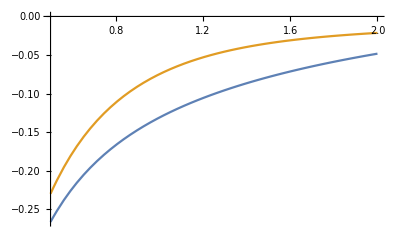

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[{20,11,3},α],Log[Zα]-logSymmetric3NoDiag[{20,11,3},α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->0.5}
```

-1.45982

```mathematica
Log[Zα]/.{α->5}
```

Log[693809375]

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}],{mat,Cases[allMats[[goodPos]],x_/;Total[Diagonal[x]]==20]}];
```

```mathematica
ZαDiag/.{α->1}
```

3

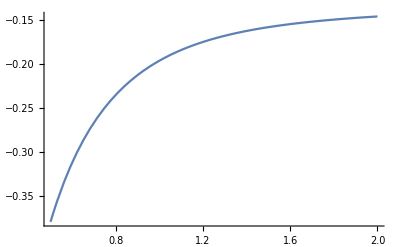

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[{20,11,3},20,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

1.09861

```mathematica
ZαDiag/.{α->5}//N//Log
```

18.4677

1.09861, 18.4677

#### Case 2

```mathematica
tk= {3,3,3,3,2,2};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

16

6

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

3108105

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

3108105

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

1828

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

1828

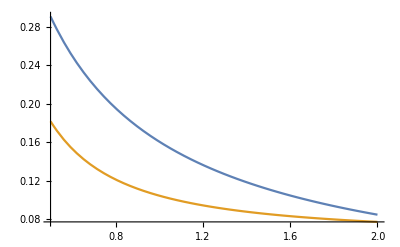

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

7.51098

```mathematica
Log[Zα]/.{α->5}//N
```

19.8828

7.51098, 19.8828

```mathematica
diagonalSum=10;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

16

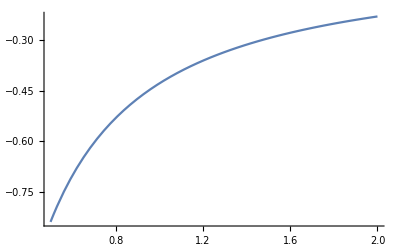

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

2.77259

```mathematica
ZαDiag/.{α->5}//N//Log
```

15.6481

2.77259, 15.6481

#### Case 3

```mathematica
tk= {2,2,2,2};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

8

4

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

715

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

715

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

17

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,Length[matsWithMargin[[1]]]}],{i,1,Length[matsWithMargin[[1]]]}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,Length[matsWithMargin[[1]]]}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

17

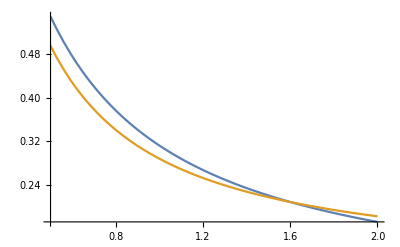

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

2.83321

```mathematica
Log[Zα]/.{α->5}//N
```

8.97778

```mathematica
diagonalSum=4;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,Length[matsWithMargin[[1]]]}],{i,1,Length[matsWithMargin[[1]]]}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,Length[matsWithMargin[[1]]]}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

6

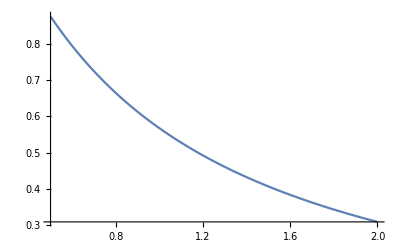

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

1.79176

```mathematica
ZαDiag/.{α->5}//N//Log
```

7.71869

1.79176, 7.71869

This is a tricky casae, there are diagonal sums where there is not a valid matrix although it is iwthin the hard support range. Need to detect this.

#### Case 4

```mathematica
tk= {2,2,2,2,2,2};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

12

6

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

230230

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

230230

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

388

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

388

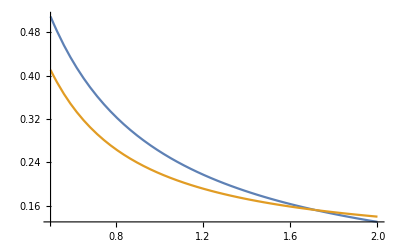

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

5.96101

```mathematica
Log[Zα]/.{α->5}//N
```

15.3585

5.96101, 15.3585

```mathematica
diagonalSum=6;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

20

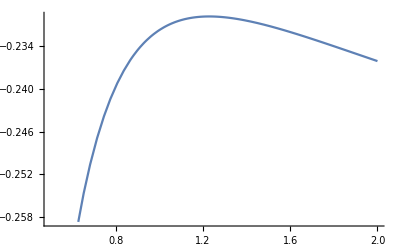

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

2.99573

```mathematica
ZαDiag/.{α->5}//N//Log
```

12.6524

2.99573, 12.6524

```mathematica
Exp[Table[logSymmetric2Diag[tk,2*mIn,1]//N,{mIn,0,Total[tk]/2}][[{1,2,3,4,5,7}]]]//Total
```

387.046

```mathematica
logSymmetric2Diag[tk,12,1]//N
```

-3.82717

#### Loading matrices found by SIS

```mathematica
SISmatsRaw="0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
1 0 0 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 2 0 0 0 
0 1 0 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 1 0 1 0 0 

0 0 1 1 0 0 
0 0 0 0 2 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 2 0 0 0 0 
0 0 1 1 0 0 

0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

0 0 0 1 1 0 
0 0 1 1 0 0 
0 1 0 0 1 0 
1 1 0 0 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 0 1 0 0 1 
0 0 1 1 0 0 
1 1 0 0 0 0 
0 1 0 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
1 0 0 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 0 0 1 0 1 
2 0 0 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 0 0 1 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

0 0 0 1 0 1 
0 0 1 0 0 1 
0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 0 1 1 0 
0 1 1 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 2 0 0 

0 0 0 0 0 2 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
2 0 0 0 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 0 0 1 0 1 
0 0 0 1 1 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 0 1 0 
0 1 0 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 0 0 0 0 2 
0 0 1 0 1 0 
0 1 0 0 1 0 
0 0 0 2 0 0 
0 1 1 0 0 0 
2 0 0 0 0 0 

0 0 2 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
1 0 1 0 0 0 
1 0 1 0 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 1 0 0 
0 0 1 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 0 1 0 1 
0 0 0 0 2 0 
0 0 0 1 0 1 
1 0 1 0 0 0 
0 2 0 0 0 0 
1 0 1 0 0 0 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 0 0 2 0 
0 0 1 1 0 0 
0 1 0 0 0 1 
0 1 0 0 0 1 
2 0 0 0 0 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 0 0 1 
0 0 0 0 1 1 
0 1 0 1 0 0 
0 0 1 1 0 0 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 0 0 0 2 
0 1 0 0 1 0 
0 1 0 1 0 0 
0 0 2 0 0 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 0 2 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 2 0 0 0 
0 0 0 0 1 1 
0 1 0 1 0 0 
0 1 0 1 0 0 

0 0 1 1 0 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 0 1 1 0 0 
0 0 0 1 0 1 
1 0 0 0 1 0 
1 1 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 0 1 1 0 0 
0 0 0 1 0 1 
1 0 0 0 0 1 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

0 0 0 0 1 1 
0 0 0 1 1 0 
0 0 0 1 0 1 
0 1 1 0 0 0 
1 1 0 0 0 0 
1 0 1 0 0 0 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 1 1 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 0 1 0 1 
0 1 1 0 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 1 0 0 
0 0 1 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 0 1 0 1 
0 0 0 1 0 1 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 0 1 0 
0 0 0 0 0 2 
1 0 1 0 0 0 
0 0 0 2 0 0 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 1 0 0 
0 0 1 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

0 0 2 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 0 0 0 2 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 2 0 0 

0 0 1 0 0 1 
0 0 0 1 1 0 
1 0 0 0 0 1 
0 1 0 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 0 0 2 0 
0 1 0 0 0 1 
0 0 2 0 0 0 
0 1 0 1 0 0 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 0 1 1 0 
0 0 1 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 1 0 0 1 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 2 0 0 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 0 0 1 1 
1 0 0 0 0 1 
0 0 0 2 0 0 
1 1 0 0 0 0 
0 1 1 0 0 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 0 0 2 0 
0 1 0 0 0 1 
0 0 2 0 0 0 
1 0 0 1 0 0 

0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 2 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 0 2 0 0 0 
0 0 0 0 1 1 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 0 1 1 0 
1 0 1 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 
0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 2 0 0 0 

0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 0 1 0 0 
1 0 1 0 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 1 0 0 0 
0 1 0 1 0 0 

0 0 1 0 0 1 
0 0 0 1 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

0 0 0 1 1 0 
0 0 1 1 0 0 
0 1 0 0 0 1 
1 1 0 0 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 1 1 0 0 
0 0 0 0 1 1 
1 0 0 0 0 1 
1 0 0 0 1 0 
0 1 0 1 0 0 
0 1 1 0 0 0 

0 0 0 0 2 0 
0 0 0 1 0 1 
0 0 2 0 0 0 
0 1 0 0 0 1 
2 0 0 0 0 0 
0 1 0 1 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 1 0 0 
0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 0 0 1 1 
0 2 0 0 0 0 
1 0 1 0 0 0 
1 0 1 0 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
1 0 1 0 0 0 

0 0 0 0 2 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 0 1 1 0 
0 1 1 0 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 0 0 1 
0 0 0 0 1 1 
0 1 0 1 0 0 
0 0 1 1 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 0 1 0 1 
1 0 1 0 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 0 0 1 
0 0 0 2 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 1 0 1 0 0 

0 0 0 0 0 2 
0 0 0 1 1 0 
0 0 0 1 1 0 
0 1 1 0 0 0 
0 1 1 0 0 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 1 0 0 
0 0 1 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
0 2 0 0 0 0 

0 0 1 1 0 0 
0 0 1 0 1 0 
1 1 0 0 0 0 
1 0 0 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

0 0 1 0 1 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 1 0 1 0 0 

0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 0 1 0 
1 0 0 0 0 1 
0 1 1 0 0 0 
1 0 0 1 0 0 

0 0 0 0 2 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 1 1 0 0 0 

0 0 2 0 0 0 
0 0 0 1 1 0 
2 0 0 0 0 0 
0 1 0 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 0 1 0 1 0 
0 0 0 0 0 2 
1 0 0 1 0 0 
0 0 1 0 1 0 
1 0 0 1 0 0 
0 2 0 0 0 0 

0 0 1 0 0 1 
0 0 0 0 2 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 2 0 0 0 0 
1 0 1 0 0 0 

0 0 0 1 1 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
2 0 0 0 0 0 
0 0 1 1 0 0 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

0 0 0 0 1 1 
0 0 1 0 1 0 
0 1 0 0 0 1 
0 0 0 2 0 0 
1 1 0 0 0 0 
1 0 1 0 0 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 0 0 1 1 
0 0 1 0 0 1 
0 1 0 1 0 0 
0 0 1 0 1 0 
1 0 0 1 0 0 
1 1 0 0 0 0 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

0 0 0 2 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 1 1 0 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 0 0 2 
1 0 1 0 0 0 
0 0 0 2 0 0 

0 0 1 0 1 0 
0 0 0 1 1 0 
1 0 0 0 0 1 
0 1 0 0 0 1 
1 1 0 0 0 0 
0 0 1 1 0 0 

0 0 0 2 0 0 
0 0 0 0 1 1 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 1 0 1 0 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 0 1 0 1 
0 0 1 0 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 0 0 1 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

0 0 0 1 1 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 2 0 0 0 0 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 1 0 0 
0 0 1 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 0 1 1 0 
0 0 0 1 0 1 
0 0 2 0 0 0 
1 1 0 0 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 1 1 0 0 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 0 1 0 0 1 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
1 1 0 0 0 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 0 0 1 1 
1 0 0 0 0 1 
0 1 1 0 0 0 
0 0 1 1 0 0 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 1 0 0 
0 0 1 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 1 0 1 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

0 0 0 1 1 0 
0 0 0 0 0 2 
0 0 0 1 1 0 
1 0 1 0 0 0 
1 0 1 0 0 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 2 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 1 1 0 0 
0 0 1 0 1 0 
1 1 0 0 0 0 
1 0 0 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 0 1 1 0 
1 0 1 0 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
1 1 0 0 0 0 
0 0 2 0 0 0 

0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 

0 0 1 1 0 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 1 1 0 0 
0 0 1 1 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 0 0 2 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
1 0 0 1 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 2 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 0 0 1 1 0 
0 0 0 1 0 1 
0 0 0 0 1 1 
1 1 0 0 0 0 
1 0 1 0 0 0 
0 1 1 0 0 0 

0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 0 1 0 
0 1 0 0 0 1 
1 0 1 0 0 0 
1 0 0 1 0 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 0 1 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 
0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
1 1 0 0 0 0 
0 0 0 2 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 

0 0 0 1 1 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 1 1 0 0 0 

0 0 0 0 2 0 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 0 0 1 1 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
1 1 0 0 0 0 
1 0 0 1 0 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 0 1 0 
0 0 0 0 1 1 
0 0 1 1 0 0 
1 0 0 1 0 0 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 0 0 2 0 0 
0 0 1 0 1 0 
0 1 0 0 1 0 
2 0 0 0 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 0 0 1 1 
0 0 0 1 1 0 
1 0 1 0 0 0 
0 1 1 0 0 0 
1 1 0 0 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 0 1 0 1 
0 0 1 1 0 0 
0 1 0 0 1 0 
1 1 0 0 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 0 1 0 0 1 
0 0 0 0 1 1 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 1 1 0 0 0 
1 1 0 0 0 0 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 2 0 0 0 
0 0 0 0 1 1 
0 1 0 1 0 0 
1 0 0 1 0 0 

0 0 0 1 1 0 
0 0 0 1 1 0 
0 0 0 0 0 2 
1 1 0 0 0 0 
1 1 0 0 0 0 
0 0 2 0 0 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 0 1 0 1 
0 1 1 0 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
1 0 0 1 0 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 0 1 1 0 
1 0 1 0 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 0 0 1 1 
0 0 1 0 0 1 
0 1 0 0 1 0 
0 0 0 2 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 0 1 1 0 
0 1 1 0 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 0 0 1 
0 1 0 0 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 

0 0 0 1 1 0 
0 0 0 0 1 1 
0 0 2 0 0 0 
1 0 0 0 0 1 
1 1 0 0 0 0 
0 1 0 1 0 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 1 1 0 0 

0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 2 0 0 0 
0 0 0 2 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 

0 0 0 1 0 1 
0 0 1 0 0 1 
0 1 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 1 0 
1 0 0 1 0 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 0 1 
1 0 1 0 0 0 
1 0 0 1 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 0 1 1 0 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 2 0 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 0 1 0 1 0 
0 0 1 0 1 0 
1 1 0 0 0 0 
0 0 0 0 0 2 
1 1 0 0 0 0 
0 0 0 2 0 0 

0 0 1 0 0 1 
0 0 0 1 0 1 
1 0 0 0 1 0 
0 1 0 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 

0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 

0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 
1 0 0 1 0 0 
1 0 1 0 0 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 0 1 1 0 
1 0 1 0 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
1 0 0 1 0 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 0 1 1 
0 0 1 1 0 0 
1 0 0 1 0 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
1 0 0 0 0 1 
1 0 1 0 0 0 
0 0 1 1 0 0 

0 0 1 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 
0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 
0 0 0 2 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 0 1 0 
0 0 0 2 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 0 2 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 
2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 0 1 0 
0 0 0 2 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 1 0 0 
0 0 1 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 0 0 1 1 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 0 1 0 0 1 
0 0 1 0 1 0 
1 1 0 0 0 0 
0 0 0 0 1 1 
0 1 0 1 0 0 
1 0 0 1 0 0 

0 0 2 0 0 0 
0 0 0 1 1 0 
2 0 0 0 0 0 
0 1 0 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 0 1 0 1 
1 0 1 0 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 0 0 0 2 
1 0 0 0 1 0 
0 0 0 2 0 0 
1 0 1 0 0 0 
0 2 0 0 0 0 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 1 0 1 
0 1 1 0 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 1 0 0 1 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 0 0 1 0 
1 0 0 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 1 1 0 0 0 
1 0 1 0 0 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 1 0 0 
0 0 1 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 0 1 1 0 0 
0 0 0 1 1 0 
1 0 0 0 1 0 
1 1 0 0 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 0 1 0 
0 0 0 0 0 2 
0 1 1 0 0 0 
0 0 0 2 0 0 

0 0 1 0 0 1 
0 0 1 0 1 0 
1 1 0 0 0 0 
0 0 0 2 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

0 0 1 0 0 1 
0 0 1 1 0 0 
1 1 0 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 2 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 2 0 0 

0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 2 0 0 0 
0 1 0 0 1 0 
1 0 0 1 0 0 
1 1 0 0 0 0 

0 0 0 1 0 1 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 1 1 0 0 
0 0 1 1 0 0 

0 0 1 0 1 0 
0 0 1 0 1 0 
1 1 0 0 0 0 
0 0 0 2 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 0 0 1 1 
0 1 0 0 1 0 
0 0 1 1 0 0 
0 1 1 0 0 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 0 1 
0 0 0 2 0 0 
1 0 0 0 1 0 
0 2 0 0 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 0 0 0 2 
0 0 0 1 1 0 
0 0 2 0 0 0 
0 1 0 0 1 0 
0 1 0 1 0 0 
2 0 0 0 0 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 
0 0 1 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 0 0 1 
1 0 0 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 0 2 0 0 
1 0 0 0 1 0 
0 2 0 0 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
1 0 1 0 0 0 

0 0 2 0 0 0 
0 0 0 1 0 1 
2 0 0 0 0 0 
0 1 0 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 1 1 0 0 
0 0 0 0 0 2 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 
0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
0 2 0 0 0 0 
0 0 1 1 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 1 1 0 0 
0 0 0 1 1 0 
1 0 0 0 0 1 
1 1 0 0 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 0 1 0 1 
1 0 1 0 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 
0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 1 0 0 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 1 0 0 0 
1 0 0 1 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 0 1 0 
0 0 0 0 0 2 
0 1 1 0 0 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 1 0 0 
0 0 0 0 0 2 
1 0 0 0 1 0 
1 0 0 0 1 0 
0 0 1 1 0 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 2 0 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 2 0 0 0 
0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

0 0 0 0 2 0 
0 0 1 0 0 1 
0 1 0 1 0 0 
0 0 1 0 0 1 
2 0 0 0 0 0 
0 1 0 1 0 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 
0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 0 1 0 0 1 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
1 1 0 0 0 0 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 0 1 
0 0 0 1 0 1 
1 0 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
1 1 0 0 0 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 0 1 0 
0 1 0 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 0 1 0 
0 0 0 2 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 

0 0 1 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 
0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 1 0 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 0 0 1 1 
0 1 0 0 1 0 
0 0 1 1 0 0 
1 0 1 0 0 0 

0 0 0 0 1 1 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 2 0 0 

0 0 1 1 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 

0 0 1 1 0 0 
0 0 0 0 2 0 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 0 0 0 1 1 
2 0 0 0 0 0 
0 0 0 0 1 1 
0 1 0 1 0 0 
0 1 0 1 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 0 0 0 2 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 1 0 0 
0 0 1 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 0 0 0 0 2 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
2 0 0 0 0 0 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 1 1 
0 1 0 0 0 1 
1 0 1 0 0 0 
0 0 1 1 0 0 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 1 1 0 0 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 0 0 1 1 
0 1 0 0 0 1 
0 1 1 0 0 0 
0 0 1 1 0 0 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 1 1 0 0 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 0 0 1 1 
1 0 0 0 1 0 
0 0 1 1 0 0 
1 0 1 0 0 0 

0 0 0 2 0 0 
0 0 0 0 1 1 
0 0 0 0 1 1 
2 0 0 0 0 0 
0 1 1 0 0 0 
0 1 1 0 0 0 

0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 0 1 0 1 
0 1 1 0 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

0 0 0 0 1 1 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
1 0 0 1 0 0 

0 0 2 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 1 1 0 0 
0 1 0 0 1 0 
0 1 0 0 1 0 
0 0 1 1 0 0 
2 0 0 0 0 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 0 0 1 1 
0 0 0 2 0 0 
1 0 1 0 0 0 
0 1 1 0 0 0 

0 0 0 0 2 0 
0 0 0 1 0 1 
0 0 0 1 0 1 
0 1 1 0 0 0 
2 0 0 0 0 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 

0 0 0 1 1 0 
0 0 1 0 1 0 
0 1 0 0 0 1 
1 0 0 0 0 1 
1 1 0 0 0 0 
0 0 1 1 0 0 

0 0 0 2 0 0 
0 0 1 0 1 0 
0 1 0 0 0 1 
2 0 0 0 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 0 0 1 1 
1 1 0 0 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 0 1 0 
0 1 0 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 1 1 0 0 
0 1 0 0 0 1 
1 1 0 0 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 
0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 1 0 0 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 1 1 0 0 
0 0 1 1 0 0 

0 0 0 1 0 1 
0 0 0 0 2 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 2 0 0 0 0 
1 0 0 1 0 0 

0 0 2 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 2 0 0 0 0 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 0 0 1 1 
1 0 0 0 1 0 
0 0 1 1 0 0 
0 1 1 0 0 0 

0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 1 1 0 
0 1 1 0 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 2 0 0 0 
0 1 0 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 0 1 0 
0 1 0 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 1 0 
0 0 0 1 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 0 1 1 0 0 
0 0 0 0 1 1 
1 0 0 0 1 0 
1 0 0 0 0 1 
0 1 1 0 0 0 
0 1 0 1 0 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 
0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 

0 0 0 1 1 0 
0 0 0 1 1 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
2 0 0 0 0 0 

0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 0 1 0 1 
0 0 0 0 2 0 
1 1 0 0 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 

0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 1 0 0 
0 1 1 0 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 0 0 0 2 
1 0 0 0 1 0 
0 1 0 1 0 0 
0 0 2 0 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 2 0 0 0 
1 0 0 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

0 0 0 1 0 1 
0 0 0 0 1 1 
0 0 2 0 0 0 
1 0 0 0 1 0 
0 1 0 1 0 0 
1 1 0 0 0 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 2 0 0 0 
0 1 0 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 0 1 0 1 
0 0 0 1 1 0 
0 0 0 0 1 1 
1 1 0 0 0 0 
0 1 1 0 0 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

0 0 1 1 0 0 
0 0 1 1 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 0 1 
0 0 0 1 1 0 
1 0 0 0 1 0 
0 1 0 0 0 1 
0 1 1 0 0 0 
1 0 0 1 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2";
```

#### Analysis

```mathematica
SISmatsRaw1=ToExpression[StringSplit[StringSplit[SISmatsRaw,"\n"]," "]];
```

```mathematica
SISmats=Table[SISmatsRaw1[[7*(i-1)+1;;7*(i-1)+6]],{i,1,Length[SISmatsRaw1]/7+1}];
```

```mathematica
SISmats//Length
```

387

```mathematica
matsWithMargin//Length
```

388

Finding the examples of matrices which are not being generated by the sampler

There are examples of cases where there is a

```mathematica
Total[Diagonal[#]]&/@SISmats//Tally
```

{{4,90},{2,108},{6,20},{0,130},{8,15},{12,1}}

```mathematica
notFoundMatrices=Complement[matsWithMargin,SISmats];
```

```mathematica
Diagonal/@notFoundMatrices
```

{{2,2,2,2,2,2}}

```mathematica
MatrixForm/@notFoundMatrices
```

{(2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2)}

Found (m_in = 1):

```mathematica
MatrixForm/@Cases[SISmats,x_/;x[[1,1]]==2&&Total[Diagonal[x]]==2]
```

{(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 2
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 2 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 2 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 2 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 2
0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0)}

Not found:

```mathematica
MatrixForm/@Cases[notFoundMatrices,x_/;x[[1,1]]==2]
```

{(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0)}

Computing the true marginal probabilities in this case

```mathematica
Cases[matsWithMargin,x_/;x[[1,1]]==2&&Total[Diagonal[x]]==2]//Length
```

22

```mathematica
Cases[matsWithMargin,x_/;x[[1,1]]==2&&Total[Diagonal[x]]==2][[;;,3,2]]
```

{2,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0}

So this probability should be 1/22..

```mathematica
marginPieces=Cases[matsWithMargin,x_/;x[[1,1]]==2&&Total[Diagonal[x]]==2][[;;,3;;,2]];
```

So, we need to count over the possible

```mathematica
Tally[marginPieces]
```

{{{2,0,0,0},1},{{1,1,0,0},3},{{1,0,1,0},3},{{1,0,0,1},3},{{0,2,0,0},1},{{0,1,1,0},3},{{0,1,0,1},3},{{0,0,2,0},1},{{0,0,1,1},3},{{0,0,0,2},1}}

```mathematica
logSymmetric2Diag[{2,2,2,2}-{1,0,1,0},0,1.00001]//Re
```

1.10466

```mathematica
logSymmetric2Diag[{2,2,2,2}-{2,0,0,0},0,1.00001]//Re
```

0.293729

#### Checking the off-diagonal counts

Hopefully this has been implemented correctly, so that we can now try to reproduce this in the c++ code

```mathematica
diagonalSum=2;
```

```mathematica
tmOut=(Total[tk]-diagonalSum)/2;
```

```mathematica
tmIn=diagonalSum/2;
```

```mathematica
tn=Length[tk];
```

```mathematica
αSymmetric2Diag[2*tmOut,Length[diagonalSum],0,1+0.00001]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
ths = Table[Module[{di,binom,α},di=sThis-sPrev;α=αSymmetric2Diag[2*tmOut,Length[diagonalSum],0,1]+0.00001;binom=Binomial[tk[[i]]-2 di+α-1,α-1];binom*If[(i==1&&sPrev!=0)||(i==tn&&sThis!=tmIn),0,1]*If[0<=tk[[i]]-2 di<=tmOut&&di>=0,1,0]],{i,1,tn},{sPrev,0,tmOut},{sThis,0,tmOut}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}}

```mathematica
tgs=Table[ths[[i,sPrev+1,sThis+1]]If[i==tn,1,Sum[ths[[i+1,sThis+1,sNext+1]],{sNext,0,tmOut}]],{i,1,tn},{sPrev,0,tmOut},{sThis,0,tmOut}]
```

{{{-5199462,-7807,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{60660390,288859,0,0,0},{0,60660390,288859,0,0},{0,0,60660390,287490,0},{0,0,0,60372900,0},{0,0,0,0,0}},{{0,-7770,-24642,0,0},{0,0,-5174820,-2443665,0},{0,0,0,-513169650,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,1,0},{0,0,0,666,0},{0,0,0,66045,0},{0,0,0,0,0}}}

Computing the transition probabilities P(s_i|s_{i-1})

```mathematica
tps=Table[tgs[[i,sPrev+1,sThis+1]]/Module[{s},s=Sum[tgs[[i,sPrev+1,t+1]],{t,0,tmOut}];If[s==0,1,s]],{i,1,tn},{sPrev,0,tmOut},{sThis,0,tmOut}]
```

{{{666/667,1/667,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{210/211,1/211,0,0,0},{0,210/211,1/211,0,0},{0,0,211/212,1/212,0},{0,0,0,1,0},{0,0,0,0,0}},{{0,35/146,111/146,0,0},{0,0,36/53,17/53,0},{0,0,0,1,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,1,0},{0,0,0,1,0},{0,0,0,1,0},{0,0,0,0,0}}}

```mathematica
tps[[-2]]//MatrixForm//N
```

(0. | 0.239726 | 0.760274 | 0. | 0.
0. | 0. | 0.679245 | 0.320755 | 0.
0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

Sample from these transitions

```mathematica
tRandS={};tp=1;
Module[{sNext},sNext=RandomChoice[tps[[1,0+1]]->Table[s,{s,0,tmOut}]];AppendTo[tRandS,sNext];tp*=tps[[1,0+1,sNext+1]];Do[sNext=RandomChoice[tps[[i,tRandS[[-1]]+1]]->Table[s,{s,0,tmOut}]];tp*=tps[[i,tRandS[[-1]]+1,sNext+1]];AppendTo[tRandS,sNext];,{i,2,tn}]]
{tRandS,tp}
```

{{0,0,1,3},2447550/10273801}

#### Case 5

```mathematica
tk= {2,2,1,1,1,1};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

8

6

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

10626

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

10626

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

36

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

36

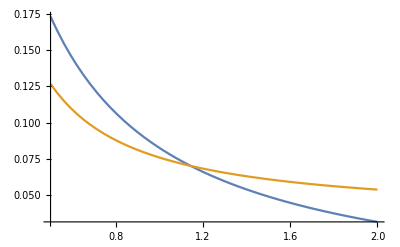

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

3.58352

```mathematica
Log[Zα]/.{α->5}//N
```

9.98737

2.70805, 7.53636

```mathematica
diagonalSum=6;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

0

```mathematica
Log[388]//N
```

5.96101

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

-Graphics-

```mathematica
ZαDiag/.{α->1}//N//Log
```

Indeterminate

```mathematica
ZαDiag/.{α->5}//N//Log
```

Indeterminate

2.99573, 12.6524

### count_asymmetric_matrix

### count_binary_matrix

## Moment matching validation

### alpha_symmetric_2

#### diagonal_sum = None

```mathematica
αSymmetric2NoDiag[T_,n_,α_]:= (T+(1+n) (-2+n (-1+T)+T) α)/(2 (-1+T)+n (-2+T+α+n α))
```

```mathematica
αSymmetric2NoDiag[200,10,1]//N
```

9.75402

```mathematica
αSymmetric2NoDiag[200,10,5]//N
```

41.168

#### diagonal_sum

```mathematica
αSymmetric2Diag[T_,Td_,n_,α_]:=-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))
```

```mathematica
αSymmetric2Diag[200,100,10,1]//N
```

3.6041

```mathematica
αSymmetric2Diag[200,100,10,5]//N
```

13.1526

### alpha_symmetric_3

#### diagonal_sum = None

```mathematica
αSymmetric3NoDiag[T_,n_,α_]:={(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}
```

```mathematica
αSymmetric3NoDiag[200,10,1]//N
```

{13.7998,7.53246}

```mathematica
αSymmetric3NoDiag[200,10,5]//N
```

{63.6326,30.4128}

#### diagonal_sum

### alpha_symmetric_block_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_symmetric_block_3

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_3

#### diagonal_sum = None

#### diagonal_sum

## Sequential Importance Sampling

### Symmetric

```mathematica
validMin[ks_]:=Module[{m},m=Total[ks]/2;Flatten[Table[If[Total[Ceiling[(ks-(m-mIn))/2]]<=mIn,mIn,{}],{mIn,0,m}]]]
```

#### sample_diagonal_sum

Possible m_in (note that this is not necessarily a continuous range):

```mathematica
tk = {2,2,2,2};
```

```mathematica
tk = {3,3,3,3,2,2};
```

```mathematica
validMin[tk,Total[tk]/2]
```

{0,1,2,3,4,5,6,7}

Adding some to the alpha to avoid divergences

```mathematica
Table[αSymmetric2Diag[Total[tk],2*mIn,Length[tk],1+0.0000001],{mIn,validMin[tk]}]
```

{16.5,11.598,6.79851,4.07576,2.60013,1.75377,1.23473,0.897163}

```mathematica
diagValProbs = Table[Re[logSymmetric2Diag[tk,2*mIn,1+0.0000001]],{mIn,validMin[tk]}]//Exp
```

{324.742,619.863,538.022,281.498,99.2114,24.5501,4.20982,0.459237}

Associated entropy:

```mathematica
tDiagSum=7;
```

```mathematica
-Log[diagValProbs[[tDiagSum+1]]/Total[diagValProbs]]
```

8.32387

Note that some of these cases have negative alpha values... That’s a bit problematic but should be ok for the SIS

#### sample_diagonal_entries

#### sample_off_diagonal_table

### Asymmetric

### Symmetric binary matrices

Since the Erdos-Gallai condition does not (as far as I can tell) factor nicely as the estimate does. Therefore we must adopt an alternative strategy.

```mathematica
erdosGallaiCondition[ks_]:=Module[{ksSorted,n},n=Length[ks];ksSorted=Reverse[Sort[ks]];And@@Table[Sum[ksSorted[[i]],{i,1,l}]<=l(l-1)+Sum[Min[ksSorted[[i]],l],{i,l+1,n}],{l,1,n}]]
```

```mathematica
tk={5,3,3,2,2,1,1};
```

```mathematica
erdosGallaiCondition[tk]
```

True

## Workspace

### alpha_symmetric_2

#### diagonal_sum = None

Convert to the c++ format

```mathematica
αSymmetric2NoDiag[2 m,n,α]
```

(2 m+(1+n) (-2+2 m+(-1+2 m) n) α)/(2 (-1+2 m)+n (-2+2 m+α+n α))

2nd central moments of the Dirichlet-Multinomial distribution with total t and length n, we want n → n(n+1)/2 here:

-Graphics-

```mathematica
secondCentralMoment = t/n(n α + t)/(n α + 1)(d - n^(-1));
```

In order to compute the covariances of the degrees this is going to be sum over a variety of contirbutions. We can split into two cases:

i = j:

```mathematica
1+2*(n - 1)+(n-1) + (n-1)(n-2)//Simplify
```

n^2

```mathematica
4*1*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1}) +2*2*(n - 1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})+(n-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1}) + (n-1)(n-2)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})//Simplify
```

((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))

```mathematica
(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}/.{αM->αSymmetric2NoDiag[T,n,1]}//FullSimplify)==(((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1})
```

((-1+n) (2+n) T (n+n^2+T))/(n^2 (1+n) (2+n+n^2))==((-2+n+n^2) T (n (1+n)+T))/(n^2 (1+n) (2+n+n^2))

```mathematica
Solve[(((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1})==secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM},αM]//FullSimplify
```

{{αM→(-n (3+n)+2 (-1+T)+n (2+n) T)/(2 (-1+T)+n (-1+n+T))}}

```mathematica
Solve[((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))==(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}),αM]//FullSimplify
```

{{αM→(T+(1+n) (-2+n (-1+T)+T) α)/(2 (-1+T)+n (-2+T+α+n α))}}

i != j:

```mathematica
1 + 1 + 2(n-1) + ((n-1)^2-1)//Simplify
```

n^2

```mathematica
1 *(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1})+ 1 *(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})*4+ 2(n-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})*2 + ((n-1)^2-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})//Simplify
```

-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))

```mathematica
((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/(-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α)))//Simplify
```

1-n

```mathematica
αSymmetric2NoDiag[t,n,1]
```

```mathematica
-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1}/.{T->34,n->3}
```

-1955/126

#### diagonal_sum

Convert to the c++ format

```mathematica
αSymmetric2Diag[2 m,2m mu, n,α]
```

-((4 m^2 mu^2 (-1+n) (2+(-1+n) n α)+4 m mu (-1+n) n α (2+(-1+n) n α)-4 m^2 (-1+n) (1+n α) (2+(-1+n) n α)+(2 m-2 m mu) (-2+n) (1+n α) (2 m-2 m mu+(-1+n) n α))/(n (4 m^2 mu^2 (-1+n) (2+(-1+n) n α)+4 m mu (-1+n) n α (2+(-1+n) n α)-2 m (-1+n) (1+n α) (2+(-1+n) n α)+(2 m-2 m mu) (-2+n) (1+n α) (2 m-2 m mu+(-1+n) n α))))

11:

```mathematica
1+2*(n - 1)+(n-1) + (n-1)(n-2)//Simplify
```

n^2

```mathematica
4*1*(secondCentralMoment/.{t->Td/2,n->n,d->1}) +2*2*(n - 1)*0+(n-1)*(secondCentralMoment/.{t->To/2,n->n(n-1)/2,d->1}) + (n-1)(n-2)*(secondCentralMoment/.{t->To/2,n->n(n-1)/2,d->0})//Simplify
```

(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2

```mathematica
(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2/.{α->1,n->3,To->14,Td->20}
```

295/9

```mathematica
αMrule=Solve[(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2==(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}),αM][[1]]//FullSimplify
```

{αM→-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) To (1+n α) (To+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) To (1+n α) (To+(-1+n) n α))))}

```mathematica
αM/.αMrule/.{To->T - Td}//Simplify
```

-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))

22:

### alpha_symmetric_3

third moment of DM:

```mathematica
thirdCentralMoment = t/n(n α + t)(n α + 2 t)/((n α + 1)(n α + 2))(d3 - d2/n + 2/n^2);
```

#### diagonal_sum = None

111:

```mathematica
1+3(n-1)+3(n-1)+3(n-1)(n-2)+(n-1)(n-2)(n-3)+3(n-1)(n-2)+n-1//Simplify
```

n^3

```mathematica
1(thirdCentralMoment /.{d3->1,d2->3}/.{t->T/2,n->n(n+1)/2})*8+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*4+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*2+3(n-1)(n-2)(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*2+(n-1)(n-2)(n-3)*(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*1+3(n-1)(n-2)*(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*1+(n-1)*(thirdCentralMoment /.{d3->1,d2->3}/.{t->T/2,n->n(n+1)/2})*1//Simplify
```

((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))

```mathematica
((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))/.{α->1,T->34,n->3}
```

1955/27

```mathematica
1/2((thirdCentralMoment/.{d3->1,d2->3,t->T}/.{α->alphaMinus})+(thirdCentralMoment/.{d3->1,d2->3,t->T}/.{α->alphaPlus}))/.{T->34,n->3}//Simplify
```

1955/27

```mathematica
Solve[{((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

{{αP→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),αM→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)},{αP→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),αM→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}}

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)/.{α->1,T->200,n->10}//N
```

13.7998

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)/.{Sqrt[a_]->0}//FullSimplify
```

(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)

```mathematica
denominator=
```

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/.{T->200,n->10,α->1}
```

6820008328

#### diagonal_sum

111:

```mathematica
1+3(n-1)+3(n-1)+3(n-1)(n-2)+(n-1)(n-2)(n-3)+3(n-1)(n-2)+n-1//Simplify
```

n^3

```mathematica
1(thirdCentralMoment /.{d3->1,d2->3}/.{t->Td/2,n->n})*8+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*0+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*0+3(n-1)(n-2)(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*0+(n-1)(n-2)(n-3)*(thirdCentralMoment /.{d3->0,d2->0}/.{t->To/2,n->n(n-1)/2})*1+3(n-1)(n-2)*(thirdCentralMoment /.{d3->0,d2->1}/.{t->To/2,n->n(n-1)/2})*1+(n-1)*(thirdCentralMoment /.{d3->1,d2->3}/.{t->To/2,n->n(n-1)/2})*1//Simplify
```

(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))

```mathematica
(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))/.{α->1,n->3,To->14,Td->20}
```

2273/27

```mathematica
Solve[{(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

$Aborted

```mathematica
Solve[{((8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))/.{α->1})==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),((((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2/.{α->1})==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

$Aborted

### alpha_symmetric_block_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_symmetric_block_3

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_3

#### diagonal_sum = None

#### diagonal_sum